```mathematica
(*2. Считать данные из полученного входного файла в системе Wolfram Mathematica (учесть, что размерность графа может быть любой и параметры bi могут идти в произвольном порядке).*)
```

```mathematica
inFileName=StringJoin[NotebookDirectory[],"input.txt"];
fileStream=OpenRead[inFileName];
Is=Read[fileStream,{Word,Number}][[2]];
Us=Read[fileStream,{Word,Number}][[2]];
U=ReadList[fileStream,Expression,Us];
weight=ReadList[fileStream,String,Is];
weight=Sort[Table[StringSplit[weight[[i]],{"b","_","/*","*/ ", " "}], {i,Is}]];
UDirect=Table[U[[i,1]]->U[[i,2]],{i,Us}]
Close[fileStream];
```

{1->2,3->1,1->4,5->2,1->6,3->6,3->7,4->3,5->3,5->6,6->2,7->1,7->4}

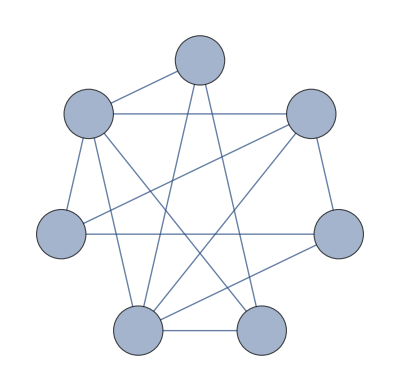

```mathematica
(*3. По полученным данным создать ориентированный граф с заданием стилей/*)
g = Graph[UDirect, GraphLayout->"CircularEmbedding", VertexLabels->Placed["Name",Center], VertexSize->0.4, VertexLabelStyle-> Directive[Italic, 28], EdgeShapeFunction->GraphElementData["FilledArrow","ArrowSize"->0.05], EdgeStyle->Thick]
```

```mathematica
(*4. Построить матрицу инцидентности для полученного графа.*)
(m=IncidenceMatrix[g])//MatrixForm;
```

## Лабораторная 3.

```mathematica
(*3. написать функцию построения системы уравнений баланса для заданного графа с использованием функционального подхода/*)
edges=Subscript[x,#]&/@UDirect;
equations=ConstantArray[0,Is];
equations=Fold[With[{i=First[Last[#2]],j=Last[Last[#2]]}, ReplacePart[#1,{i->#1[[i]]+#2,j->#1[[j]]-#2}]]&,equations,edges];
equations//TableForm;
equationsSystem=equations[[#]]==ToExpression[weight[[#]][[2]]]&/@Range[Is];
equationsSystem//TableForm
```

x_(1->2)+x_(1->4)+x_(1->6)-x_(3->1)-x_(7->1)==2
-x_(1->2)-x_(5->2)-x_(6->2)==-6
x_(3->1)+x_(3->6)+x_(3->7)-x_(4->3)-x_(5->3)==-4
-x_(1->4)+x_(4->3)-x_(7->4)==-1
x_(5->2)+x_(5->3)+x_(5->6)==3
-x_(1->6)-x_(3->6)-x_(5->6)+x_(6->2)==3
-x_(3->7)+x_(7->1)+x_(7->4)==3

```mathematica
(*1. Используя процедурный подход, написать функцию построения системы баланса в узлах графа.*)
equations=ConstantArray[0,Is];
For[i=1,i<=Us,i++,{t=UDirect[[i]],equations[[t[[1]]]]+=Subscript[x,t],equations[[t[[2]]]]-=Subscript[x,t]}];
equationsSystem=ConstantArray[0,Is];
For[i=1,i≤Is,i++,equationsSystem[[i]]=equations[[i]]==ToExpression[weight[[i]][[2]]]];
equationsSystem//TableForm
```

x_(1->2)+x_(1->4)+x_(1->6)-x_(3->1)-x_(7->1)==2
-x_(1->2)-x_(5->2)-x_(6->2)==-6
x_(3->1)+x_(3->6)+x_(3->7)-x_(4->3)-x_(5->3)==-4
-x_(1->4)+x_(4->3)-x_(7->4)==-1
x_(5->2)+x_(5->3)+x_(5->6)==3
-x_(1->6)-x_(3->6)-x_(5->6)+x_(6->2)==3
-x_(3->7)+x_(7->1)+x_(7->4)==3

```mathematica
(*2. Решить полученную систему функцией Solve и проверить правильность решения функцией Simplify (функцией упрощения системы, после подстановки в нее полученного решения).*)
s=Solve[equationsSystem]
Simplify[equationsSystem/.s[[1]]]
```

{{x_(4->3)→4-x_(1->2)-x_(1->6)+x_(3->1)+x_(3->7),x_(5->3)→x_(1->2)+x_(1->6)+x_(3->6),x_(5->6)→3-x_(1->2)-x_(1->6)-x_(3->6)-x_(5->2),x_(6->2)→6-x_(1->2)-x_(5->2),x_(7->1)→-2+x_(1->2)+x_(1->4)+x_(1->6)-x_(3->1),x_(7->4)→5-x_(1->2)-x_(1->4)-x_(1->6)+x_(3->1)+x_(3->7)}}

{True,True,True,True,True,True,True}